## Computer practise 1. Group 2: Nerea Andia, Ander Cano, Mikel Lamela and Aitor Larrinoa

## OPTIONAL

## 2. The Lotka-Volterra model.

### c) Write a program in Mathematica that shows the evolution of the populations of foxes and rabbits, correspondent to A = 0.5, B = 0.002, C = 0.1, D = 0.001 and initial population of 250 rabbits and 100 foxes.

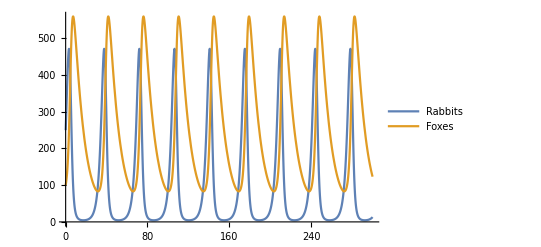

```mathematica
sol=NDSolve[{x'[t]==0.5*x[t]-0.002*x[t]*y[t], y'[t]==-0.1*y[t]+0.001*x[t]*y[t], x[0]==250,y[0]==100},{x,y},{t,0,300}];
Plot[{Evaluate[{x[t]}/.sol],Evaluate[{y[t]}/.sol]},{t,0,300},PlotLegends->{"Rabbits","Foxes"}]
```